{A,P,P,L,E}

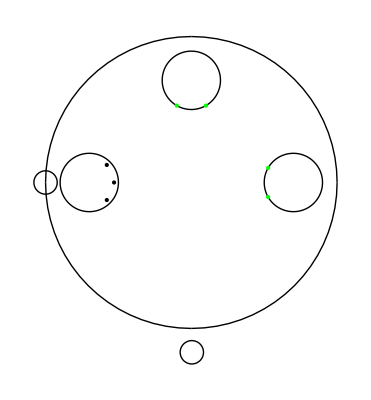

```mathematica
Clear["Global`*"]
Needs["GallifreyanLetters`"]
(*
lGraph[bounds_]:=Graphics[{{Red,Dashed,Circle[wordPosition,wordSize]},Circle[wordPosition,wordSize,bounds]}];
lGraph[#]&/@edges;

getSpacing[word_]:=chooseSpacing[#]&/@StringPartition[word//ToUpperCase,1];
getWordSize[word_]:=If[StringLength[word]<5,1,Total[getSpacing[word]]/(2Pi)];
centerPoint1[x_]:=If[StringLength[word]<5,.54,0.8253195827576976-0.11060277353478278 x+0.007703034792707071 x^2-0.00026579896491144955 x^3+3.570865399323157*^-6 x^4];
*)

inputString="apple";

(* Calculate constants from input string*)
word=inputString//ToUpperCase;
wordPosition={0,0};
wordSize=1;
letterSize=0.2;
wordLength= StringLength[word]-StringCount[word,{"CH","SH","TH","NG","QU"}];
lettersList=StringPartition[word,1];
lettersListLength=Array[Plus,wordLength,1];

letterPositionsList={};
(* end *)

(* Position & edge functions *)
edgePoint[offset_,rA_,rB_]:=(1-rB/rA)offset;
edgePoints[edgeInfo_,centerL_,radiusW_,radiusL_]:= edgeInfo[[1]][centerL]+edgePoint[edgeInfo[[2]],radiusW,radiusL]*{1,-1};
fixRightEdge[edge_]:=If[edge[[2]]≥0,edge,edge+{0,2Pi}];
fixLeftEdge[edge_]:=If[(edge[[1]]-edge[[2]])≤ 2Pi,edge,edge-{2Pi,0}];
letterPositions[wordLength1_]:=CirclePoints[wordPosition,{wordSize,(3Pi)/2},wordLength1];
(* end *)

(* Functions for translating English to Gallifreyan *)
translationNeeded[pos_]:=If[(pos+1)≤wordLength&&((lettersList[[pos]]=="C"&&lettersList[[pos+1]]=="H")||
						 (lettersList[[pos]]=="S"&&lettersList[[pos+1]]=="H")||
						 (lettersList[[pos]]=="T"&&lettersList[[pos+1]]=="H")||
						 (lettersList[[pos]]=="N"&&lettersList[[pos+1]]=="G")||
						 (lettersList[[pos]]=="Q"&&lettersList[[pos+1]]=="U")),True,False];
translateC[l_]:=If[l=="C","K",l];
counter1=0;
translateToGallifreyan[word_]:=If[ translationNeeded[++counter1],
lettersList[[counter1]]<>lettersList[[++counter1]],
lettersList[[counter1]]];
isVowelAfterConsonant[pos_]:=If[isVowel[lettersList[[pos]]]&&!isVowel[lettersList[[pos-1]]]&&pos≠1,True,False];
(* end *)

(* Translate English to Gallifreyan *)	
lettersList=translateC[#]&/@translateToGallifreyan[word]&/@lettersListLength
convertedToLetters=chooseLetter[#]&/@lettersList;
convertedToEdges=chooseEdge[#]&/@lettersList;
(* end *)


countVowels[letters_]:=Total[If[isVowel[#],1,0]&/@letters];
countSoloVowels[letters_]:=Count[If[isVowel[letters[[#]]]&&!isVowelAfterConsonant[#],True,False]&/@lettersListLength,True];
countConsonants[word1_]:=wordLength-countVowels[lettersList]+countSoloVowels[lettersList];
numOfConsonants=countConsonants[word];

(* dup position if vowel follows constant *)
counter2=0;
letterPositionsList=Flatten[Append[letterPositionsList,letterPositions[numOfConsonants][[If[isVowelAfterConsonant[#],counter2,++counter2]]]]&/@lettersListLength,1];
(* end *)

edgesList=If[isVowelAfterConsonant[#],Nothing,convertedToEdges[[#]]]&/@lettersListLength;

lettersOutput=Partition[Riffle[convertedToLetters,letterPositionsList],2];
edgesOutput=Partition[Riffle[edgesList,letterPositions[numOfConsonants]],2];

(* Print letters and edges *)
printLetter[letter_,pos_]:=letter[pos,letterSize];
letters=printLetter[#[[1]],#[[2]]]&/@lettersOutput;
edges=edgePoints[#[[1]],#[[2]],wordSize,letterSize]&/@edgesOutput;
(* end *)

(* Calculate edge points of letters *)
addCircleIfNoEdges[edges_]:=If[Length[edges]==0,{{0,2Pi}},edges];
preAdjustEdges[edges_]:=If[Length[edges]==1,edges,fixRightEdge[#]&/@edges];
sortEdges[edges_]:=Partition[Insert[TakeDrop[edges,1][[1]]//Flatten,Reverse[TakeDrop[edges,1][[2]]//Flatten],-2]//Flatten,2];
postAdjustEdges[edges_]:=If[Length[edges]==1,edges,fixLeftEdge[#]&/@edges];
placeOnWord[edges_]:=Circle[wordPosition,wordSize,#]&/@edges;
calculateEdges[edges_]:=placeOnWord[postAdjustEdges[sortEdges[preAdjustEdges[addCircleIfNoEdges[edges]]]]];
edges=calculateEdges[edges];
(* end *)

(* Display letters and edges *)
Graphics[{letters,edges}]
(* end *)


take2[list_]:=Take[list,2]
drop1[list_]:=Drop[list,1]
isVowelAfterConsonant2[prevL_,currL_]:=If[!isVowel[prevL]&&isVowel[currL],True,False];
```

```mathematica
(*
data={{4,.49},{5,.435},{6,.385},{7,.345},{8,.313},{9,.283},{10,.26},{11,.24},{12,.222},{16,.172},{20,.14},{24,.118}};
gp=ListPlot[data,PlotRange->{{0,26},{0,.5}}];
fit1=Fit[data,{1,x,x^2,x^3,x^4},x];
Plot[%,{x,0,25}];
Show[%,gp];
*)
Graphics[Arrow[{{0,0},#}]&/@CirclePoints[{1,(3Pi)/2},3],Frame->True];
Graphics[Arrow[{{1,1},#}]&/@CirclePoints[{1,1},{1,(3Pi)/2},3],Frame->True];

list={"A","A","A","A"};
list=Insert[list,"B",{{2},{4}}];


x=1;
int1=6;
int2=5;

If[x>0,If[int1>5,int1=0,int1];5,int2]
int1
```

5

0